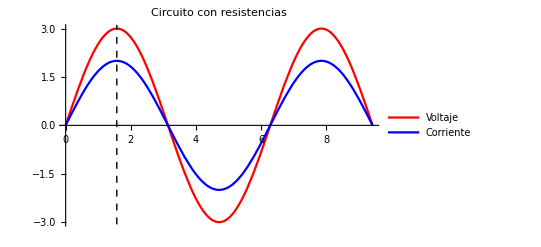

```mathematica
Plot[{3Sin[x],2Sin[x ]} , {x, 0, 3 Pi}, PlotLabel->Style["Circuito con resistencias", Black, 14],  PlotLegends->Placed[{"Voltaje", "Corriente"}, Right],PlotStyle->{Red, Blue}, Epilog->{{Dashed,Line[{{Pi/2,-3.5},{Pi/2,3.5}}]}}]
```

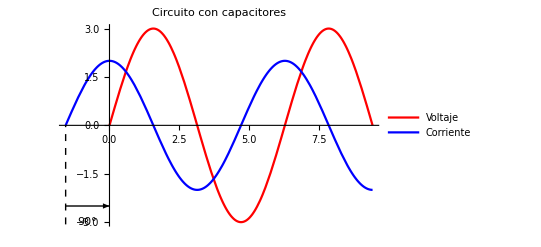

```mathematica
p1=Plot[3Sin[x],{x,0, 3 Pi}, PlotStyle->Red, PlotLegends->LineLegend[{Red},{"Voltaje"}]];
p2=Plot[2Sin[x+(Pi/2)],{x,-Pi/2, 3 Pi}, PlotStyle->Blue, PlotLegends->LineLegend[{Blue},{"Corriente"}]];
Show[p1, p2, PlotRange->All, PlotLabel->Style["Circuito con capacitores", Black, 14],Epilog->{{Dashed,Line[{{-Pi/2,-3.5},{-Pi/2,0}}]}, Arrow[{{-Pi/2, -2.5},{0,-2.5}}], Text["90°",{-0.8, -3}]}]
```

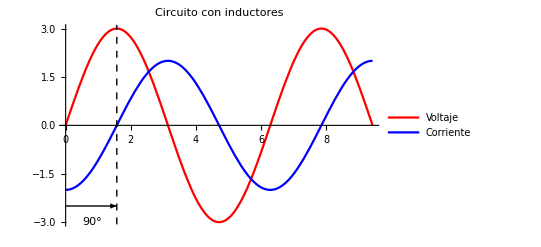

```mathematica
Plot[{3Sin[x], 2Sin[x+ (Pi/2)]},{x,0, 3 Pi} , PlotLabel->Style["Circuito con capacitores", Black, 14],  PlotLegends->Placed[{"Voltaje", "Corriente"}, Right], PlotStyle->{Red, Blue},  Epilog->{{Dashed,Line[{{Pi/2,-3.5},{Pi/2,3.5}}]}, Arrow[{{0, -2.5},{Pi/2,-2.5}}],Text["90°",{0.8, -3}]}]
```

```mathematica
Plot[{3Sin[x], 2Sin[x+ (Pi/2)]},{x,-Pi/2, 3 Pi} , PlotLabel->Style["Circuito con capacitores", Black, 14],  PlotLegends->Placed[{"Voltaje", "Corriente"}, Right], PlotStyle->{Red, Blue},  Epilog->{{Dashed,Line[{{Pi/2,-3.5},{Pi/2,3.5}}]}, Arrow[{{0, -2.5},{Pi/2,-2.5}}],Text["90°",{0.8, -3}]}]
```